```mathematica
Play[Sin[2Pi*440x],{x,0,5}]
```

-Graphics-

```mathematica
Play[Sin[2Pi*440x]+Sin[2Pi*880x],{x,0,5}]
```

-Graphics-

```mathematica
Play[Sin[2Pi*440x]+Sin[2Pi*880x]+Sin[2Pi*1760x],{x,0,5}]
```

-Graphics-

```mathematica
Play[Sin[2Pi*440x]+Sin[2Pi*550x],{x,0,5}]
```

-Graphics-

```mathematica
Play[Sin[2Pi*440x]+Sin[2Pi*441x],{x,0,5}]
```

-Graphics-

#### Triangular Wave

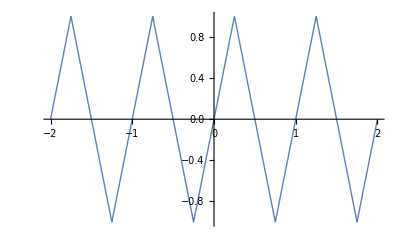

```mathematica
g[x_]:=TriangleWave[x];
Plot[g[x],{x,-2,2},PlotStyle->Thick]
```

```mathematica
Play[g[2Pi*440x],{x,0,5}]
```

-Graphics-

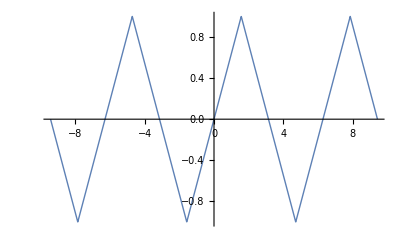

```mathematica
f[x_]:=TriangleWave[x/(2Pi)];
Plot[f[x],{x,-3*Pi,3*Pi},PlotStyle->Thick]
```

```mathematica
b[n_]:=1/π(∫_-π^(-π/2) (-2/π(x+π))*Sin[n*x] ⅆx +∫_(-π/2)^(π/2) 2/π x*Sin[n*x] ⅆx +∫_(π/2)^π (-2/π(x-π))*Sin[n*x]ⅆx)
```

```mathematica
b[3]
```

-8/(9 π^2)

```mathematica
F[x_,n_]:=∑_(k=1)^n b[k]sin[k*x]
```

```mathematica
F[x,20]
```

(8 sin[x])/π^2-(8 sin[3 x])/(9 π^2)+(8 sin[5 x])/(25 π^2)-(8 sin[7 x])/(49 π^2)+(8 sin[9 x])/(81 π^2)-(8 sin[11 x])/(121 π^2)+(8 sin[13 x])/(169 π^2)-(8 sin[15 x])/(225 π^2)+(8 sin[17 x])/(289 π^2)-(8 sin[19 x])/(361 π^2)

```mathematica
G[x_,n_]:=∑_(k=1)^n ((-1)^(k+1)*8)/((2k-1)^2*π^2)*Sin[(2k-1)*x]
```

```mathematica
G[x,10]
```

(8 Sin[x])/π^2-(8 Sin[3 x])/(9 π^2)+(8 Sin[5 x])/(25 π^2)-(8 Sin[7 x])/(49 π^2)+(8 Sin[9 x])/(81 π^2)-(8 Sin[11 x])/(121 π^2)+(8 Sin[13 x])/(169 π^2)-(8 Sin[15 x])/(225 π^2)+(8 Sin[17 x])/(289 π^2)-(8 Sin[19 x])/(361 π^2)

```mathematica
Manipulate[Plot[{f[x],G[x,n]},{x,-3π,3π},PlotStyle->{{Thick,Red},{Thick,Blue}}],{n,1,10,1}]
```

#### Energy of f

```mathematica
1/π∫_-π^π (f[x])^2 ⅆx
```

#### Energy Spectrum of f

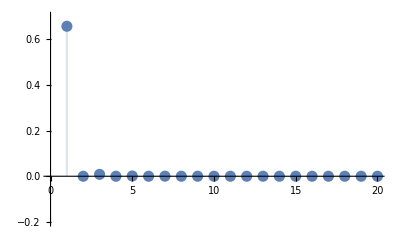

```mathematica
DiscretePlot[b[n]^2,{n,1,20},PlotRange->{-.2,.7},PlotStyle->PointSize[.02],AxesOrigin->{0,0}]
```

```mathematica
∑_(k=1)^∞ b[k]^2
```

#### A Square Wave

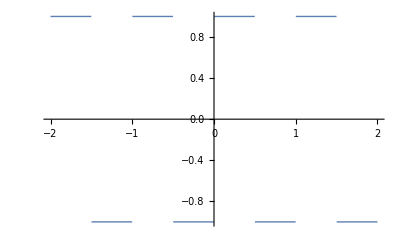

```mathematica
Clear["Global`*"]
g[x_]:=SquareWave[x];
Plot[g[x],{x,-2,2},PlotStyle->Thick]
```

```mathematica
Play[g[2π*440x],{x,0,5}]
```

-Graphics-

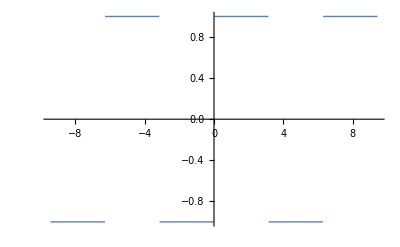

```mathematica
f[x_]:=SquareWave[x/(2π)];
Plot[f[x],{x,-3π,3π},PlotStyle->Thick]
```

```mathematica
b[n_]:=1/π(∫_-π^0 -1*Sin[n*x] ⅆx +∫_0^π 1*Sin[n*x] ⅆx )
```

```mathematica
b[7]
```

4/(7 π)

```mathematica
F[x_,n_]:=∑_(k=1)^n b[k]*Sin[k*x]
```

```mathematica
F[x,20]
```

(4 Sin[x])/π+(4 Sin[3 x])/(3 π)+(4 Sin[5 x])/(5 π)+(4 Sin[7 x])/(7 π)+(4 Sin[9 x])/(9 π)+(4 Sin[11 x])/(11 π)+(4 Sin[13 x])/(13 π)+(4 Sin[15 x])/(15 π)+(4 Sin[17 x])/(17 π)+(4 Sin[19 x])/(19 π)

```mathematica
G[x_,n_]:=∑_(k=1)^n 4/((2k-1)*π)*Sin[{2k-1}*x]
```

```mathematica
G[x,10]
```

{(4 Sin[x])/x+(4 Sin[3 x])/(3 x)+(4 Sin[5 x])/(5 x)+(4 Sin[7 x])/(7 x)+(4 Sin[9 x])/(9 x)+(4 Sin[11 x])/(11 x)+(4 Sin[13 x])/(13 x)+(4 Sin[15 x])/(15 x)+(4 Sin[17 x])/(17 x)+(4 Sin[19 x])/(19 x)}

```mathematica
Manipulate[Plot[{f[x],G[x,n]},{x,-3π,3π},PlotStyle->{{Thick,Red},{Thick,Blue}}],{n,1,20,2}]
```

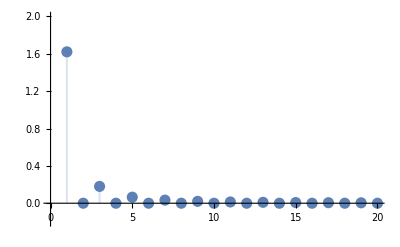

```mathematica
DiscretePlot[b[n]^2,{n,1,20},PlotRange->{-.2,2.},PlotStyle->PointSize[.02],AxesOrigin->{0,0}]
```

#### A Sawtooth Wave

```mathematica
Clear["Global`*"]
g[x_]:=SawtoothWave[x];
```

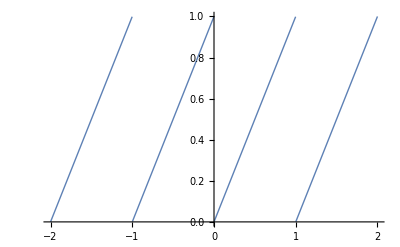

```mathematica
Plot[g[x],{x,-2,2},PlotStyle->Thick]
```

```mathematica
Play[g[2π*440x],{x,0,5}]
```

-Graphics-

```mathematica
f[x_]:=2π*(SawtoothWave[(x-π)/(2π)]-1/2);
```

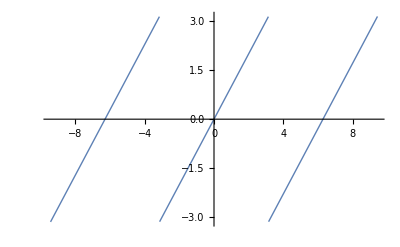

```mathematica
Plot[f[x],{x,-3π,3π},PlotStyle->Thick]
```

```mathematica
b[n_]:=1/π(∫_-π^π f[x]*Sin[n*x]ⅆx)
```

```mathematica
F[x_,n_]:=∑_(k=1)^n b[k]*Sin[k*x]
```

```mathematica
F[x,20]
```

2 Sin[x]-Sin[2 x]+2/3 Sin[3 x]-1/2 Sin[4 x]+2/5 Sin[5 x]-1/3 Sin[6 x]+2/7 Sin[7 x]-1/4 Sin[8 x]+2/9 Sin[9 x]-1/5 Sin[10 x]+2/11 Sin[11 x]-1/6 Sin[12 x]+2/13 Sin[13 x]-1/7 Sin[14 x]+2/15 Sin[15 x]-1/8 Sin[16 x]+2/17 Sin[17 x]-1/9 Sin[18 x]+2/19 Sin[19 x]-1/10 Sin[20 x]

```mathematica
G[x_,n_]:=∑_(k=1)^n (2*(-1)^(k+1))/k*Sin[k*x]
```

```mathematica
G[x,20]
```

2 Sin[x]-Sin[2 x]+2/3 Sin[3 x]-1/2 Sin[4 x]+2/5 Sin[5 x]-1/3 Sin[6 x]+2/7 Sin[7 x]-1/4 Sin[8 x]+2/9 Sin[9 x]-1/5 Sin[10 x]+2/11 Sin[11 x]-1/6 Sin[12 x]+2/13 Sin[13 x]-1/7 Sin[14 x]+2/15 Sin[15 x]-1/8 Sin[16 x]+2/17 Sin[17 x]-1/9 Sin[18 x]+2/19 Sin[19 x]-1/10 Sin[20 x]

```mathematica
Manipulate[Plot[{f[x],G[x,n]},{x,-3π,3π},PlotStyle->Thick],{n,1,10,1}]
```

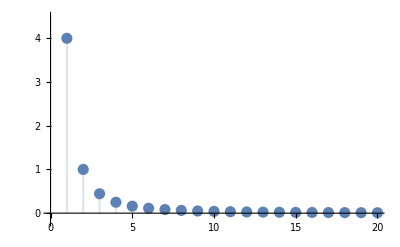

```mathematica
DiscretePlot[b[n]^2,{n,1,20},PlotRange->{-.2,4.5},PlotStyle->PointSize[.02],AxesOrigin->{0,0}]
```